# Functions for Graph-Rewriting Automata

Paul Cousin

## Functions

### Utilities

```mathematica
aliveColor=RGBColor[0.5, 0, 0.5];deadColor=RGBColor[1, 0.5, 0];unknownColor = GrayLevel[1];
```

```mathematica
initialGraph={SparseArray[…],SparseArray[…]};
```

```mathematica
Options[linearAlgebraToGraph]={"3D"->False, "Size"->Medium};
linearAlgebraToGraph[{aM_,sV_},OptionsPattern[]]:= Module[{adjacencyMatrix=Normal[aM],stateVector=Normal[sV]},
Return[If[OptionValue["3D"],Graph3D[AdjacencyGraph[adjacencyMatrix,VertexStyle->Table[i->If[stateVector[[i]]==={1},aliveColor,deadColor],{i,1,Length[stateVector],1}],ImageSize->OptionValue["Size"]]],AdjacencyGraph[adjacencyMatrix,VertexStyle->Table[i->If[stateVector[[i]]==={1},aliveColor,deadColor],{i,1,Length[stateVector],1}],ImageSize->OptionValue["Size"]]]]
];

graphToLinearAlgebra[graph_]:={SparseArray[AdjacencyMatrix[IndexGraph[graph]]],SparseArray[Transpose[{SortBy[Options[IndexGraph[graph],VertexStyle]/.{VertexStyle->a_}:>a,#/.(a_->b_):>a&]/.(_->a_):>If[a===aliveColor,1,0]}]]};
```

### Rules

```mathematica
oneDivisionRules=Catenate[Table[Map[#+2^i&,Range[0,255]],{i,8,11}]];
```

```mathematica
binary[n_]:=∑_(i=0)^23 IntegerDigits[n,10,24][[-1-i]]×2^i;
```

```mathematica
rule[n_]:=Table[{If[i<=-4,aliveColor,deadColor],Mod[-i,4]}->{If[IntegerDigits[n,2,24][[i-1]]==1,aliveColor,deadColor],If[IntegerDigits[n,2,24][[i-9]]==1,True,False]},{i,-7,0}];
```

```mathematica
transformationPlot[{before_,aliveNeighbors_}->{after_,divide_}]:=GraphicsGrid[{{Graph[{0<->1,0<->2,0<->3},VertexStyle->{0->before,1->If[aliveNeighbors>0,aliveColor,deadColor],2->If[aliveNeighbors>1,aliveColor,deadColor],3->If[aliveNeighbors>2,aliveColor,deadColor]},VertexSize->0.4,ImageSize->40, GraphLayout->"RadialEmbedding"]-> If[!divide,Graph[{0<->1,0<->2,0<->3},VertexStyle->{0->after,1->unknownColor,2->unknownColor,3->unknownColor},VertexSize->0.4,ImageSize->40, GraphLayout->"RadialEmbedding"],Rotate[Graph[{10<->1,20<->2,30<->3,10<->20,20<->30,30<->10},VertexStyle->{10->after,20->after,30->after,1->unknownColor,2->unknownColor,3->unknownColor},VertexSize->0.55,ImageSize->43],180 Degree]]}},ImageSize->{128,75}];
```

```mathematica
rulePlotLabeled[n_]:=Block[{picture},Grid[{{Text[n" = "BaseForm[n,2]]},{
picture[{a_,b_,c_,d_,e_,f_,g_,h_}]:=Map[transformationPlot[#]&,{a,b,c,d,e,f,g,h}]/.{i_,j_,k_,l_,m_,o_,p_,q_}:>{{i,j,k,l},{m,o,p,q}};
GraphicsGrid[picture[rule[n]],Frame->True]
}}]];
```

```mathematica
rulePlot[n_]:=Block[{picture},Grid[{{
picture[<|a_,b_,c_,d_,e_,f_,g_,h_|>]:=Map[transformationPlot[#]&,{a,b,c,d,e,f,g,h}]/.{i_,j_,k_,l_,m_,o_,p_,q_}:>{{i,j,k,l},{m,o,p,q}};
GraphicsGrid[picture[rule[n]],Frame->True]
}}]];
```

### Evolution

```mathematica
ruleState[ruleNumber_,case_]:=IntegerDigits[ruleNumber,2,16][[-case-1]];
ruleDivision[ruleNumber_,case_]:=IntegerDigits[ruleNumber,2,16][[-case-9]];
```

```mathematica
configurationVector[{aM_,sV_}]:=Normal[4×sV+aM.sV];
```

```mathematica
newState[{aM_,sV_},ruleNumber_]:= SparseArray[Map[ruleState[ruleNumber,#]&,configurationVector[{aM,sV}]]];
```

```mathematica
evolve[{aM_,sV_},rN_,it_:1]:=Module[{divisionVector=Map[ruleDivision[rN,#]&,configurationVector[{aM,sV}]],adjacencyMatrix=aM,stateVector=newState[{aM,sV},rN],replicate,vertexNumber,state, line, ones,insert,subMatrix},

(*Function*)
replicate[v_,p_,n_]:=Nest[Insert[#,#[[p]],p]&,v,n];	

(*Loop*)
While[!FreeQ[divisionVector,1],

vertexNumber=Position[divisionVector,{1}][[1]][[1]];

(*Update state vector*)
stateVector=replicate[stateVector,vertexNumber,2];

(*First division pass on adjacency matrix*)	
line = Normal@adjacencyMatrix[[vertexNumber]];
ones = Catenate@Position[line,1];
adjacencyMatrix=Delete[adjacencyMatrix,vertexNumber];
insert=SparseArray[{{1,ones[[1]]}->1,{2,ones[[2]]}->1,{3,ones[[3]]}->1},{3,Length[line]}];
Do[adjacencyMatrix=Insert[adjacencyMatrix,insert[[i]],vertexNumber],{i,1,3}];

(*Transpose*)
adjacencyMatrix=Transpose[adjacencyMatrix];

(*Second division pass on adjacency matrix*)
line = Normal@adjacencyMatrix[[vertexNumber]];
ones = Catenate@Position[line,1];
adjacencyMatrix=Delete[adjacencyMatrix,vertexNumber];
insert=SparseArray[{{1,ones[[1]]}->1,{2,ones[[2]]}->1,{3,ones[[3]]}->1},{3,Length[line]}];
Do[adjacencyMatrix=Insert[adjacencyMatrix,insert[[i]],vertexNumber],{i,1,3}];


(*Adding the submatrix*)
adjacencyMatrix[[vertexNumber;;vertexNumber+2,vertexNumber;;vertexNumber+2]] = {{0,1,1},{1,0,1},{1,1,0}};

(*Update division vector*)
divisionVector=replicate[ReplacePart[divisionVector,vertexNumber->{0}],vertexNumber,2];
];

Return[{adjacencyMatrix,stateVector}];

];
```

## Examples

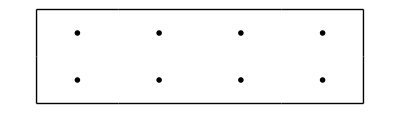
2222  =  100010101110_2
-Graphics-

```mathematica
rulePlotLabeled@binary@100010101110
```

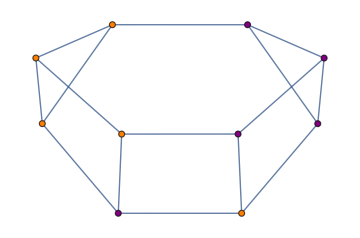

```mathematica
linearAlgebraToGraph@initialGraph
```

```mathematica
Grid@{linearAlgebraToGraph[#,"3D"->True, "Size"->Tiny]&/@NestList[evolve[#,256]&,graphToLinearAlgebra@-Graphics3D-,5],Table["t="<>ToString[i],{i,0,5}]}
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
t=0 | t=1 | t=2 | t=3 | t=4 | t=5

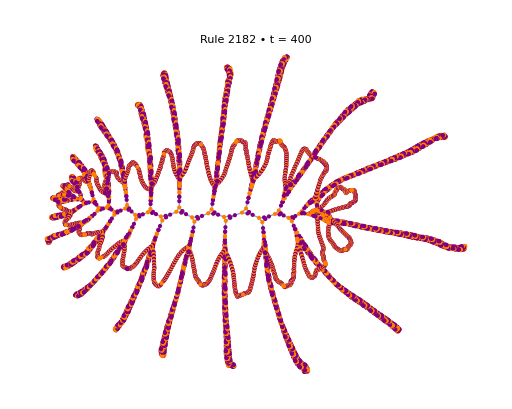

```mathematica
GraphPlot[linearAlgebraToGraph@Nest[evolve[#,2182]&,initialGraph,400], PlotLabel->"Rule 2182  •  t = 400"]
```

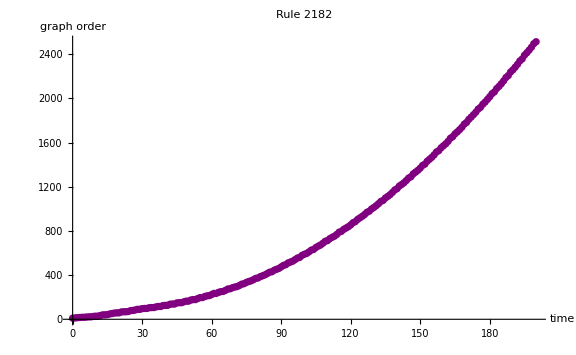

```mathematica
ListPlot[Length/@NestList[evolve[#,2182]&,initialGraph,200][[All,2]],DataRange->{0,200},PlotStyle->Purple,ImageSize->Large,AxesLabel->{"time","graph order"}, PlotLabel->"Rule 2182"]
```

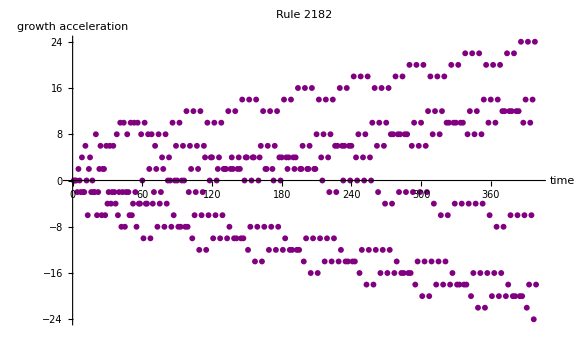

```mathematica
ListPlot[Differences@Differences@(Length/@NestList[evolve[#,2182]&,initialGraph,400][[All,2]]),PlotStyle->Purple,ImageSize->Large,AxesLabel->{"time","growth\nacceleration"}, PlotLabel->"Rule 2182"]
```

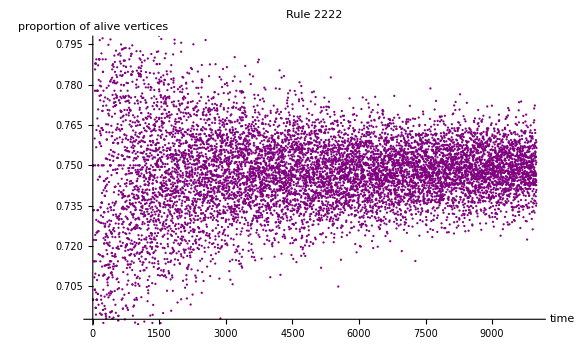

```mathematica
ListPlot[(Total[#][[1]])/Length[#]&/@NestList[evolve[#,2222]&,initialGraph,10000][[All,2]],DataRange->{0,10000},ImageSize->Large,PlotStyle->Purple, AxesLabel->{"time","proportion of\nalive vertices"}, PlotLabel->"Rule 2222"]
```

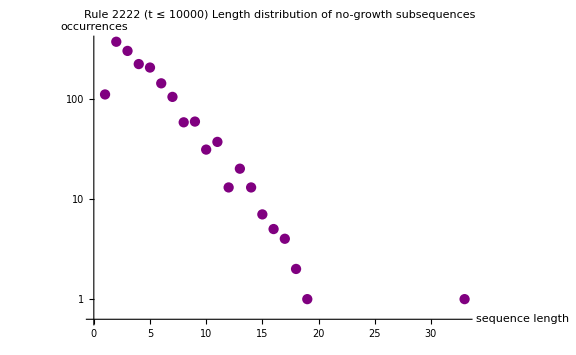

```mathematica
ListLogPlot[CountsBy[Select[Split[Differences[Length/@NestList[evolve[#,2222]&,initialGraph,10000][[All,2]]]],MemberQ[0]],Length],ImageSize->Large,PlotStyle->Purple,PlotLabel->"Rule 2222 (t ≤ 10000)\nLength distribution of no-growth subsequences",AxesLabel->{"sequence\nlength","occurrences"}]
```

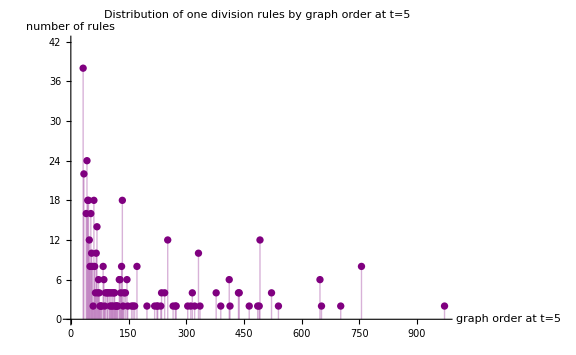

```mathematica
Block[{nestEvolve},
nestEvolve[graph_,ruleNumber_,iterations_]:=Nest[evolve[#,ruleNumber]&,graph,iterations];
ListPlot[2*Counts[Length[nestEvolve[initialGraph,#,5][[2]]]&/@oneDivisionRules],
PlotStyle->Purple,ImageSize->Large,Filling->Axis, AxesLabel->{"graph order \n at t=5","number of rules"},
PlotLabel->"Distribution of one division rules by graph order at t=5"]]
```

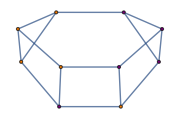
-Graphics- | Number of alive second neighbors for each vertex: | (1
3
3
1
1
2
3
2
0
2)

```mathematica
Module[{aM = initialGraph[[1]], sV = initialGraph[[2]],    clip := Clip[#, {0, 1}] &},   Grid[{{linearAlgebraToGraph[initialGraph, "Size" -> Small], "Number of alive second neighbors for each vertex:",      MatrixForm[clip/@(clip/@(aM.aM)-aM-IdentityMatrix[Length@sV]).sV]}}]]
```